```mathematica
(* ------------------------------- *)
(* Bifurcations in First-Order ODEs *)
(* ------------------------------- *)
```

```mathematica
(* A first-order autonomous ordinary differential equation (ODE) with a parameterr has the general form dx/dt=f(x,r).
The fixed points are the values of x for whichf(x,r) = 0.
A bifurcation occurs when the number or the stability of the fixed points changes as system parameters change. *)

(* The classical types of bifurcations that occur in nonlinear dynamical systems are produced from the following prototypical differential equations: *)
```

```mathematica
(* saddle:                     dx/dt=r+x^2
transcritical:               dx/dt=r x-x^2
supercritical pitchfork:     dx/dt=r x-x^3
subcritical pitchfork:     dx/dt=r x+x^3
 *)
```

```mathematica
(* This Demonstration shows bifurcations of these nonlinear first-order ODEs as you vary the parameter r *)
```

```mathematica
(* The top figure shows the phase portrait, dx/dt versus x,with stable fixed points indicated by solid disks and unstable fixed points as open circles. The bottom figure shows the solutions,x(t) versus t, starting from a number of initial states with stable fixed points indicated by solid lines and unstable fixed points as dashed lines. You can vary both the number of initial states and time duration,Subscript[t, max]. Note how the fixed points and solutions change as bifurcations occur as you vary the parameter r *)
```

```mathematica
(* ------------------- *)
(* Function Definitions *)
(* ------------------- *)
```

```mathematica
(* RHS of ODE's *)
Saddle[x_,r_]:=r+x^2
Transcritical[x_,r_]:=r*x-x^2
PitchForkSuper[x_,r_]:=r*x-x^3
PitchForkSub[x_,r_]:=r*x+x^3
```

```mathematica
(* fixed points *)
fixedPoints[f_, r_] := Solve[f[x, r] == 0, x]
```

```mathematica
(* phase portraits *)
markers={{Graphics[Disk[{0,0},1]],0.07},{Graphics[Circle[{0,0},1]],0.07}};

phasePortrait[f_,r_]:=
Show[
Plot[
f[x,r ],
{x,-1.3,1.3},
AxesLabel->{Style["x",Italic],Style["dx/dt",Italic]},
PlotStyle->Thickness[0.008]
],

ListPlot[
{{x,0}}/.fixedPoints[f,r],
PlotMarkers->markers[[ 1+UnitStep[Re[D[f[x,r], x]]/.fixedPoints[f,r]] ]]
],

Ticks->{{-1,1},{-1,1}},
PlotRange->{1.3{-1,1},1.1*{-1,1}},
AxesOrigin->{0,0},ImageSize->{370,225}
]
```

```mathematica
(* numerical solution of ODE *)
ODEsol[f_,x0_,r_,tmax_]:=
NDSolve[
{x'[t]==f[x[t],r],x[0]==x0},
x,{t,0,tmax},
AccuracyGoal->3,
PrecisionGoal->3
];
```

```mathematica
(* solution plots *)
solutionPlot[f_,x0_,r_,tmax_]:=
Module[{sol,tp},
sol=ODEsol[f,x0,r,tmax];
tp=Min[tmax,sol[[1,1,2,1,1,2]] ];
Show[
Plot[
Evaluate[x[t]/.sol],
{t,0,tp},
PlotRange->1.3{-1,1},
PlotStyle->Thickness[0.008]
],

Plot[
Evaluate[x/.fixedPoints[f,r]],
{t,0,tmax},
PlotStyle->
{{Thin,Black,If[MatchQ[Transcritical,f]||MatchQ[PitchForkSub,f],Dashing[0.01],Dashing[1]]},
{Thin,Black,If[MatchQ[Transcritical,f]||MatchQ[PitchForkSub,f],Dashing[1],Dashing[0.01]]}}
],

PlotRange->{{0,tmax},1.3{-1,1}},
AxesLabel->{Style["t",Italic],Row[{Style["x",Italic],"(",Style["t",Italic],")"}]},
Ticks->{All,Range[-10,10]},
AxesOrigin->{0,-1.3},ImageSize->{370,225}
]
];

solutionPlot[f_,{x0min_,x0max_,n_},r_,tmax_]:=
Show[Table[solutionPlot[f,x0,r,tmax],{x0,x0min,x0max,(x0max-x0min)/(n-1)}],ImageSize->{370,225}];

x0min=-1.2;
x0max=1.2;
```

```mathematica
Manipulate[
Quiet[
GraphicsColumn[
{phasePortrait[f,r],
solutionPlot[f,{x0min,x0max,n},r,tmax]},
Spacings->0
]
],

{{f,Saddle,"ODE"},{Saddle->"saddle",Transcritical->"transcritical",PitchForkSuper->"supercritical pitchfork",PitchForkSub->"subcritical pitchfork"},ControlPlacement->Top},
{{r,-1,"parameter r"},-1,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{tmax,5,"t_max"},0.1,10,.01,Appearance->"Labeled",ImageSize->Tiny},
{{n,7,"initial states"},3,21,1,Appearance->"Labeled",ImageSize->Tiny},
SaveDefinitions->True,ControlPlacement->Left,SynchronousUpdating->False,
AutorunSequencing->{{1,10},{2,10},{3,10},{4,10}}
]
```

```mathematica
(* ---------------------------------------------------------------- *)
(* Hopf Bifurcations in a Nonlinear Two-Dimensional Autonomous System *)
(* ---------------------------------------------------------------- *)
```

```mathematica
(* In the study of nonlinear dynamics,it is useful to first introduce students to simple systems that exhibit periodic behavior as a consequence of a Hopf bifurcation.The two-dimensional nonlinear and autonomous system given by: *)

ẋ=Subscript[f, 1](x,y)=-x+a y+x^2 y,
ẏ=Subscript[f, 2](x,y)=b-a y-x^2 y

(* has this feature.These equations describe the autocatalytic reaction of two intermediate speciesxandyin an isothermal batch reactor,when the system is far from equilibrium[1].In this context,the steady state referred to below is apseudo steady state,and is applicable when the precursor reactant is slowly varying with time. *)

(* The unique steady state is given bySubscript[x, S]=bandSubscript[y, S]=b/(a+b^2).This steady state is at the position of the green dot in the phase portrait diagram.It appears as the intersection of the dotted blue and green curves,which are the level curves given bySubscript[f, 1](x,y)=0andSubscript[f, 2](x,y)=0. *)

(* The stability of steady state to small disturbances can be assessed by determining the eigenvalues of the JacobianJ=({{∂Subscript[f, 1]/∂x, ∂Subscript[f, 1]/∂y}, {∂Subscript[f, 2]/∂x, ∂Subscript[f, 2]/∂y}}). A Hopf bifurcation occurs when a complex conjugate pair of eigenvalues crosses the imaginary axis. *)

(* This Demonstration shows the phase portrait with the vector field of directions around the critical point(Subscript[x, S],Subscript[y, S]).In addition,the eigenvalues ofJ,the tracetr(J),the determinant|J|,and(Δ=tr(J)))^2-4 |J|are computed.The time series are also plotted in a separate diagram (the blue and red curves correspond tox(t)andy(t),respectively.
Finally the real and imaginary parts of the two eigenvalues Subscript[λ, 1] and Subscript[λ, 2] are plotted (in blue and red,respectively) versusbfor user-specified values of the parametera. *)

(* To observe a Hopf bifurcation,you can seta=0.08and varyb.As you can see in the snapshots,there are two Hopf bifurcation points.Indeed,forb=0.3,the steady state is a stable focus;forb=0.5,the trajectory is attracted to a stable periodic solution (called a limit cycle);and finally forb=1.0,the steady state is again a stable focus.Fora=0.08,the two Hopf bifurcation points are obtained atb=0.34641andb=0.8485281374238571.Finally,the last snapshot (obtained for larger values ofa,for instance,a=0.65),the Hopf bifurcation disappears and there are only transitions from a stable node to a stable focus and then back to stable node. *)
```

```mathematica
Manipulate[Module[{f1,f2,sol,solSS,x,y,t,m,m1,sol2,p1,xx,b1,λ1,λ2,f1b1,f2b1,m2,solSSb1,Eig},

f1[x_,y_]:=-x+a*y+x^2 y;
f2[x_,y_]:=b-a*y-x^2*y;

solSS=Flatten@NSolve[{-x+a*y+x^2 y==0,b-a*y-x^2*y==0},{x,y}];


m1=Outer[D,{f1[x,y],f2[x,y]},{x,y}];

m=m1/.solSS;

Eig=Chop@N@Eigenvalues[m];

f1b1[x_,y_]:=-x+a*y+x^2 y;
f2b1[x_,y_]:=b1-a*y-x^2*y;

solSSb1=Flatten@Quiet@Solve[{-x+a*y+x^2 y==0,b1-a*y-x^2*y==0},{x,y}];

m2=Outer[D,{f1b1[x,y],f2b1[x,y]},{x,y}]/.solSSb1;

{λ1,λ2}=Eigenvalues[m2];

x0={1.25,1.25};

sol=NDSolve[{x'[t]==-x[t]+a*y[t]+x[t]^2 y[t],y'[t]==b-a*y[t]-x[t]^2*y[t],x[0]==x0[[1]],y[0]==x0[[2]]},{x,y},{t,0,500},Method-> "StiffnessSwitching"];

p1=ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,500},PlotRange->All,PlotStyle->{Black,Thickness[0.01]},PlotPoints->1000];

xx=First[Cases[p1,x_Line:> First@x,Infinity]];

Pane[Switch[ctrl,
1,
zz=Chop@N@Eigenvalues[m];

Show[
ContourPlot[{-x+a*y+x^2 y==0,b-a*y-x^2*y==0},{x,0,3},{y,0,3},
PlotLabel->Grid[Transpose@{
{"eigenvalues",If[Im[First@zz]==0,NumberForm[zz,{4,2}],Row[{Style["z",Italic]," = ",NumberForm[First@zz,{4,2}],", ",OverBar[Style["z",Italic]]}]]},
{"trace",NumberForm[Chop@N@Tr[m],{4,2}]},
{"determinant",NumberForm[Chop@N@Det[m],{4,2}]},
{"Δ",NumberForm[Chop@N@Tr[m]^2-4 Det[m],{4,2}]}},ItemSize->({#,Automatic}&/@{10,4,4,4})],
FrameLabel->{Style["x",16,Italic],Style["y",16,Italic]},PlotPoints-> 100,ContourStyle->{{Green,Thick,Dashed,Opacity[0.99]},{Blue,Dashed,Thick,Opacity[0.99]}},Epilog-> {Green,PointSize[0.025],Point[{x,y}/.solSS],Cyan,Point[x0]}],
Graphics[{Red,Arrowheads[Table[0.06,{6}]],Dashed,Thickness[0.005],Arrow[Line[Partition[xx,Floor[Length[xx/10]]][[;;;;100]]]]}],
StreamPlot[{-x+a*y+x^2 y,b-a*y-x^2*y},{x,0,3},{y,0,3},StreamStyle->Directive[Opacity[0.5]],StreamPoints-> 50],
ImageSize->400{1,1},ImagePadding->{{50,Automatic},{Automatic,Automatic}}
],
2,
Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,75},PlotRange->All,PlotStyle->{{Blue,Thick},{Red,Thick}},FrameLabel->{Style["t",16,Italic],Style[Row[{Style["x",Italic],", ",Style["y",16,Italic]}],16]},Frame-> True,GridLines->Automatic,AspectRatio->1,PlotPoints->1000,ImageSize->.9 400{1,1},ImagePadding->{{40,Automatic},{40,Automatic}}],
3,
Show[Plot[{Re[λ1],Re[λ2]},{b1,0,3},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},Frame->True,FrameLabel->{Style["b",Italic,16],Style["Re(λ)",16]},PlotRange->{{0,3},{-5,1}},GridLines->Automatic,AspectRatio-> 1],
Graphics[{RGBColor[0,0.8,0],PointSize[0.025],Point[{b,Re[Eig[[1]]]}],Point[{b,Re[Eig[[2]]]}]},ImagePadding->{{40,Automatic},{40,Automatic}}],
ImageSize->.9 400{1,1}
],
4,
Show[
Plot[{Im[λ1],Im[λ2]},{b1,0,3},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},Frame->True,FrameLabel->{Style["b",Italic,16],Style["Im(λ)",16]},PlotRange->{{0,3},{-3,3}},GridLines->Automatic,AspectRatio-> 1],
Graphics[{RGBColor[0,0.8,0],PointSize[0.025],Point[{b,Im[Eig[[1]]]}],Point[{b,Im[Eig[[2]]]}]},ImagePadding->{{40,Automatic},{40,Automatic}}],
ImageSize->.9 400{1,1}
]
],ImageSize->{500,400},Alignment->Center]],
{{a,0.8},0.01,1,0.01,Appearance-> "Labeled"},
{{b,0.062},0.01,2.5,0.001,Appearance-> "Labeled"},{{ctrl,1,""},{1-> "phase portrait",2-> "time series",3-> "real part of λ_1 and λ_2",4-> "imaginary part of λ_1 and λ_2"}},ControlPlacement->Top]
```

```mathematica
(* ------------------------------------ *)
(* Bifurcation Diagrams with Flow Fields *)
(* ------------------------------------ *)

(* 
Bifurcations indicate qualitative changes in a system's behavior.
For a dynamical system dy/dt=f(y,λ),bifurcation points are those equilibrium points at which the Jacobian(∂f)/(∂y) is singular. 

This Demonstration shows the bifurcation diagrams of several normal form bifurcations in one dimension. The bifurcation point,equilibrium points,and the flow of the vector field are visualized.The bifurcation is shown as a brown point. Solid black lines indicate stable equilibrium branches and dashed black lines indicate unstable ones. 
*)
```

```mathematica
(* ------------------- *)
(* Function Definitions *)
(* ------------------- *)
```

```mathematica
bifurcationPoints[eqn_, par_, var_]:= Cases[{par, var}/.Solve[{D[eqn, var]==0, eqn==0}, {var, par}], {Except[_Complex], Except[_Complex]}];
```

```mathematica
equilibriumCurvePlots[eqn_, {par_, parMin_, parMax_},{var_, varMin_, varmax_}]:= Module[{bifPoints, criticalPoints, parRanges, equilibriumBranches, eigenValues, stabilityCharacteristics, plotSegments},
bifPoints=bifurcationPoints[eqn, par, var];
criticalPoints= Union[{parMin, parMax}, bifPoints[[All, 1]]];
parRanges=Partition[criticalPoints, 2,1];
equilibriumBranches= Solve[eqn==0, var];
eigenValues=D[eqn, var]/.equilibriumBranches;
stabilityCharacteristics=Flatten@Map[If[Re[#]≤  0, Dashing[{}], Dashing[{0.0025,0.01}]]& , Outer[(#1/.par-> #2)&, eigenValues, Mean /@parRanges], {2}];
plotSegments=Distribute[{var/.equilibriumBranches, parRanges}, List];
MapThread[Plot[#1[[1]], Evaluate@Join[{par}, #1[[2]]],PlotStyle-> {Black, Thick,#2}]&, {plotSegments, stabilityCharacteristics}]
]
```

```mathematica
normalForms={ {"saddle node bifurcation", λ-y^2},{"transcritical bifurcation", λ y-y^2}, {"pitchfork bifurcation", λ y-y^3},  {"simple bifurcation", y^2- λ^2},{"isola center",( y^2+λ^2)}, {"hysteresis point", y^3+λ}};
```

```mathematica
Manipulate[
eqn=normalForms[[type, 2]];
equilibriumPoints=Quiet@Thread[{par, Select[y/.Solve[(eqn/.λ-> par)==0, y], Element[#, Reals]&]}];
Show[If[showStreamLines, StreamPlot[{0, eqn}, {λ, -3, 3}, {y, -3, 3}, StreamColorFunction-> (ColorData["TemperatureMap"][Arg[#4]]&),StreamColorFunctionScaling-> False], Plot[{},{λ, -3, 3}]], If[showEC, equilibriumCurvePlots[eqn, {λ, -3, 3}, {y, -3, 3}],Plot[{},{λ, -3, 3}]], PlotRange-> {{-3,3}, {-3,3}}, Axes-> False, AspectRatio-> 1, PlotLabel-> Style[ToString[normalForms[[type, 1]]]<>"\n equilibrium points: "<> ToString[equilibriumPoints]],Epilog-> Join[{PointSize[Large], Point /@  equilibriumPoints},{PointSize[Large],Brown}, Point /@ bifurcationPoints[eqn, λ, y]],Frame-> True, FrameLabel-> {"λ", Style["y",Italic]},ImageSize->{400,400}],
{{type,3, "dy/dt ="}, Array[Rule[#, normalForms[[#,2]]]&, Length[normalForms]] , PopupMenu}, {{par, 0, "bifurcation parameter λ"}, -3, 3,Appearance->"Lab
eled"},  {{showEC, True, "show equilibrium curves"}, {True, False}, Checkbox}, {{showStreamLines, True, "show streamlines"}, {True, False}, Checkbox}, 
ControlPlacement-> {Top, Top, Left, Left},SaveDefinitions-> True,TrackedSymbols->True]
```

```mathematica
(* ------------ *)
(* Vector Field *)
(* ------------ *)
```

```mathematica
Off[Power::"infy",∞::"indet"]
```

```mathematica
(*<<Graphics`PlotField`*)
<<VectorFieldPlots`
```

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

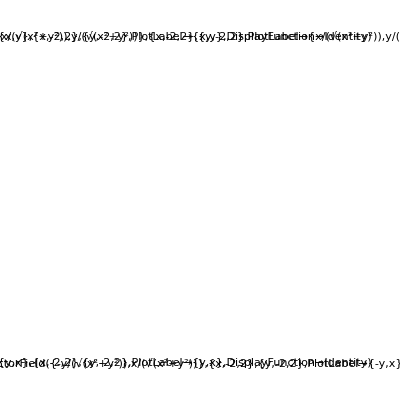

```mathematica
Show[GraphicsGrid[{{
PlotVectorField[{x,y},{x,-2,2},{y,-2,2},PlotLabel->TraditionalForm[{x,y}],DisplayFunction->Identity],
PlotVectorField[{x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]},{x,-2,2},{y,-2,2},PlotLabel->{x/Sqrt[x^2+y^2],y/Sqrt[x^2+y^2]},DisplayFunction->Identity]
},{
PlotVectorField[{y,x},{x,-2,2},{y,-2,2},PlotLabel->TraditionalForm[{y,x}],DisplayFunction->Identity],
PlotVectorField[{-y,x}/Sqrt[x^2+y^2],{x,-2,2},{y,-2,2},
PlotLabel->TraditionalForm[{-y,x}],DisplayFunction->Identity]
}
}]]
```

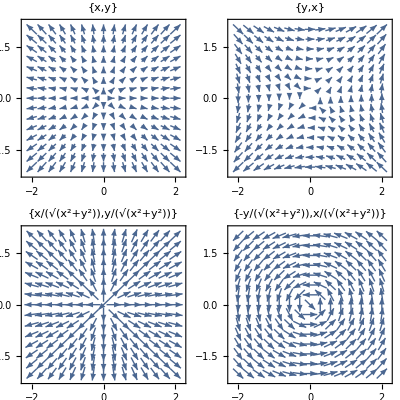

```mathematica
GraphicsGrid[Partition[VectorPlot[#,{x,-2,2},{y,-2,2},PlotLabel->#]&/@{{x,y},{y,x},{x,y}/(√(x^2+y^2)),{-y,x}/(√(x^2+y^2))},2],ImageSize->400]
```

```mathematica
(* ----------------- *)
(* Dynamical Systems *)
(* ----------------- *)
```

```mathematica
(*<<Utilities`Plot`*)
Feigenbaum=Compile[{{μ,_Real}},({μ,#}&)/@Union[Drop[NestList[μ # (1-#)&,.2,300],100]]];
```

```mathematica
f=Table[Feigenbaum[μ],{μ,3.44,3.58,.00005}];//Timing
```

{0.060257,Null}

```mathematica
ListPlot[Flatten[f,1],
PlotStyle->{Red,AbsolutePointSize[.001]},Frame->True,
FrameLabel->TraditionalForm/@{r,x},
Axes->False,PlotLabel->TraditionalForm[HoldForm[Subscript[x, n]=r Subscript[x, n-1](1-Subscript[x, n-1])]],
Prolog->{{Blue,Line[{{#,0},{#,1}}]&/@{3.44949,3.544090,3.564407,3.56875,3.56969,3.56989,3.569934,3.569943,3.5699451,3.569945557,3.569945672}}}
]
```

-Graphics-

```mathematica
ListPlot[Flatten[f,1],
PlotStyle->{Red,AbsolutePointSize[.001]},Frame->True,
FrameLabel->{r,x},
Axes->False,PlotLabel->HoldForm[Subscript[x, n]==r Subscript[x, n-1](1-Subscript[x, n-1])],
Prolog->{{Blue,Line[{{#,0},{#,1}}]&/@{3.44949,3.544090,3.564407,3.56875,3.56969,3.56989,3.569934,3.569943,3.5699451,3.569945557,3.569945672}}}
]
```

-Graphics-

```mathematica
(* --------------------- *)
(* Branches of a Function *)
(* --------------------- *)

(*<<Utilities`Plot`
<<Utilities`Typesetting`*)
```

```mathematica
Plot3D[Re[Sqrt[x+I y]],{x,-3,3},{y,-3,3},Mesh->False,PlotPoints->100,AxesLabel->TraditionalForm/@{x,y,""},PlotLabel->TraditionalForm[Re[Sqrt[z]]]
]
```

-Graphics3D-

```mathematica
(* --------------------------------------------------- *)
(* ---------------- Bifurcation Types ---------------- *)
(* --------------------------------------------------- *)
```

```mathematica
(* ---------------- *)
(* Flip Bifurcation *)
(* ---------------- *)
```

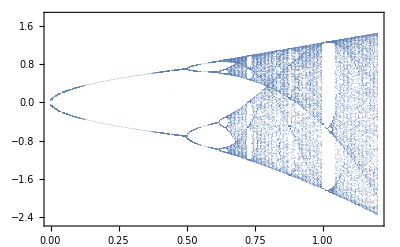

```mathematica
Feigenbaum=Compile[{{mu,_Real}},({mu,#}&) /@
			Union[Drop[NestList[mu- # (1+#)&,.2,300],100]]];

mm=Flatten[Table[Feigenbaum[mu],{mu,0.,1.2,.005}],1];

ListPlot[mm,
	PlotStyle->AbsolutePointSize[.001],Frame->True,
FrameStyle->GrayLevel[.5],Axes->False,
PlotRange->{-2.5,1.8}]
```

```mathematica
(* ---------------- *)
(* Fold Bifurcation *)
(* ---------------- *)

Feigenbaum=Compile[{{mu,_Real}},({mu,#}&) /@
			Union[Drop[NestList[mu+ # (1+#)&,.2,300],100]]];

mm=Flatten[Table[Feigenbaum[mu],{mu,0.,.1,.005}],1];

ListPlot[mm,
	PlotStyle->AbsolutePointSize[.001],Frame->True,
FrameStyle->GrayLevel[.5],Axes->False]
```

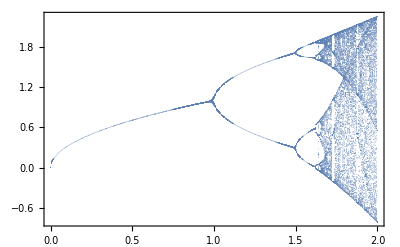

```mathematica
Feigenbaum=Compile[{{mu,_Real}},({mu,#}&) /@
			Union[Drop[NestList[mu+#- #^2&,.2,300],100]]];

mm=Flatten[Table[Feigenbaum[mu],{mu,0.,2.,.005}],1];

ListPlot[mm,
	PlotStyle->AbsolutePointSize[.001],Frame->True,
FrameStyle->GrayLevel[.5],Axes->False]
```

```mathematica
(* -------------------- *)
(* Pitchfork Bifurcation *)
(* -------------------- *)
```

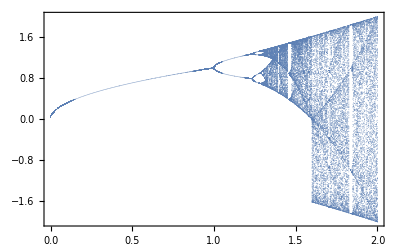

```mathematica
Feigenbaum=Compile[{{mu,_Real}},({mu,#}&) /@
			Union[Drop[NestList[mu #- #^3+#&,.2,300],100]]];

mm=Flatten[Table[Feigenbaum[mu],{mu,0.,2.,.005}],1];

ListPlot[mm,
	PlotStyle->AbsolutePointSize[.001],Frame->True,
FrameStyle->GrayLevel[.5],Axes->False]
```

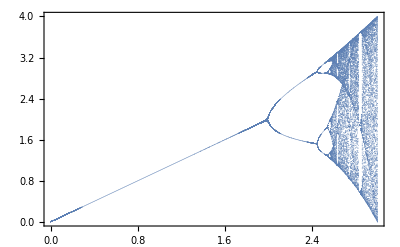

```mathematica
(* ------------------------ *)
(* Transcritical Bifurcation *)
(* ------------------------ *)

Feigenbaum=Compile[{{mu,_Real}},({mu,#}&) /@
			Union[Drop[NestList[mu #- #^2+#&,.2,300],100]]];

mm=Flatten[Table[Feigenbaum[mu],{mu,0.,3.,.005}],1];

ListPlot[mm,
	PlotStyle->AbsolutePointSize[.001],Frame->True,
FrameStyle->GrayLevel[.5],Axes->False]
```

```mathematica
(* ----- *)
(* Trigs *)
(* ----- *)
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

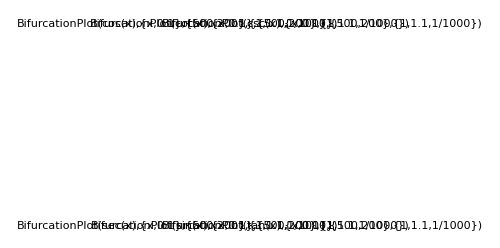

```mathematica
Show[GraphicsArray[
Partition[
Block[{$DisplayFunction=Identity},BifurcationPlot[#[x],{x,.1},{500,200},{1,1.1,10^-3}]&/@{Cos,Cot,Csc,Sec,Sin,Tan}
],3]
],ImageSize->500]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

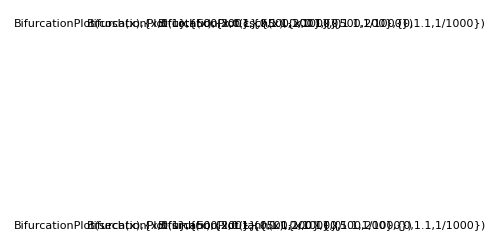

```mathematica
Show[GraphicsArray[
Partition[
Block[{$DisplayFunction=Identity},BifurcationPlot[#[x],{x,.1},{500,200},{0,1.1,10^-3}]&/@{Cosh,Coth,Csch,Sech,Sinh,Tanh}
],3]
],ImageSize->500]
```